0.0350375

0.00173156

2.54481×10^-6

6.87032×10^-11

2.59792×10^-14

2.50291

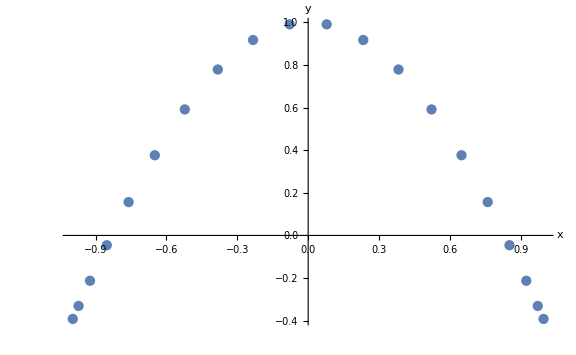

2.61458×10^-14

```mathematica
(* Determine the universal function g using a collocation method thus reducing the infinite dimensional function space to a finite vector whose elements are g evaluated at its Chebyshev nodes. We then using Arnoldi's method to find the spectrum of the linearized period doubling transformation. *)

(* define the Chebyshev nodes and period doubling transformation *)
n=20;
x=Table[Cos[((2*i-1)*Pi)/(2*n)],{i,1,n}];
ϕ[f_,x_]:=f[1]*f[x]-f[f[f[1]*x]];

(* construct f from its Chebyshev coefficients *)
gc[c_,y_]:=Sum[c[[i]]*ChebyshevT[i-1,y],{i,1,n}];

(* get the coefficients from the values of g at the Chebyshev nodes using the discrete Chebyshev transform *)
coeff[g_]:=Module[{c},

getCoeff[j_]:=2/n*Sum[g[[i]]*ChebyshevT[j-1,x[[i]]],{i,1,n}];

c=Table[getCoeff[i],{i,2,n}];
PrependTo[c,getCoeff[1]/2];
c
];

(* construct g from its Chebyshev coefficients *)
expand[g_]:=Module[{c,f},

c=coeff[g];

f[y_]:=gc[c,y];
f
];

(* construct g from its Chebyshev coefficients and evaluate it at the Chebyshev nodes *)
H[g_]:=ϕ[expand[g],x];

(* perturb the nth component of vector x by ϵ *)
perturb[x_,n_,ϵ_]:=Module[{y},
y=x;
y[[n]]=y[[n]]+ϵ;
y
];

ϵ=10^(-7);
(* approximate the Jacobian using divided differences *)
diff[g_]:=Transpose[Table[N[(H[perturb[g,i,ϵ]]-H[g])/ϵ],{i,1,n}]];

(* initialize g with a reasonable estimate *)
g={1-#1*#2^2&[1.4,x]};
it=5;

(* perform Newton's method *)
For[k=1,k≤it,k++,

A=diff[g[[k]]];

AppendTo[g,g[[k]]-Inverse[A].H[g[[k]]]];

sup=Max[Abs[g[[k+1]]-g[[k]]]];

(* we have quadratic convergence to the universal function *)
Print[sup];
]

(* α can now be determined from g *)
α=-1/expand[g[[it+1]]][1]

ListPlot[Transpose[{x,g[[it+1]]}],AxesLabel->{"x","y"},ImageSize->Large]

Max[Abs[gc[coeff[g[[it+1]]],#]-gc[coeff[g[[it]]],#]&[Range[-1,1,0.001]]]]
```

```mathematica
(* define g, the linearized period doubling transformation and 
operator the vector-valued operator M *)
γ[y_]:=gc[coeff[g[[it+1]]],y];

(* assuming α is constant *)
dF[h_,y_]:=-α*(γ'[γ[-y/α]]*h[-y/α]+h[γ[-y/α]]);

dF2[h_,y_]:=dF[h,y]-α*(γ'[γ[-y/α]]*γ'[-y/α]*y+α*γ[γ[-y/α]])*h[1];

M[g_]:=dF[gc[coeff[g],#]&,x];

(* determine the largest eigenvalue of dF by the power method *)
b=g[[it+1]];
u=Nest[M[#]/Norm[#]&,b,30];
δ=(M[u].u)/(u.u);
NumberForm[δ,8]

(* determine the (m+1)th largest eigenvalues using Arnoldi's method *)
m=n+1;
q=ConstantArray[0,{n,m+1}];
q[[All,1]]=Normalize[b];
h=ConstantArray[0,{m+1,m+1}];

For[j=1,j≤m,j++,
v=M[q[[All,j]]];
For[i=1,i≤j,i++,
h[[i,j]]=v.q[[All,i]];
v=v-h[[i,j]]*q[[All,i]];
];
h[[j+1,j]]=Norm[v];
q[[All,j+1]]=v/h[[j+1,j]];
];

NumberForm[MatrixForm[N[Round[Eigenvalues[h],12^(-8)]]],12]
(*NumberForm[MatrixForm[q],4]*)
```

4.6692016

(4.66920160946
-2.50290787727
0.999999993023
-0.399535265334
0.159628467069
-0.123652714743
-0.0637772334383
-0.0573071719779
0.0254810614078
-0.010180600804
-0.0101275311031
0.007403847721
0.00401937807139
-0.00187943581673
-0.00162513894545
-0.000259359877496
-0.0000416157249633
-7.16076993194×10^-6
-1.21167948507×10^-6
-6.0467690234×10^-8
0.
0.)